# Genetic Algorithm Non-Round Beam Optimisations

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

## β_x^*, β_y^* Round Beam Variable

Obviously these just move in step!

```mathematica
βy[βx_]:=βx;
```

```mathematica
βxβyRB=Table[{βx,βy[βx]},{βx,0,20,0.01}];
```

# Comparison of GA Non-round Beam and Round beam Optimisations

## 32 Individuals, Vary no. Generations

## F_col-ΔE_γ/E_γ Tuning Curve Plots

```mathematica
CBETAParetoFrontdat100G=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/CBETA150dat/32 Individuals/CBETA150_pareto.100","Table"];
CBETAParetoFrontdat200G=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/CBETA150dat/32 Individuals/CBETA150_pareto.200","Table"];
CBETAParetoFrontdat300G=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/CBETA150dat/32 Individuals/CBETA150_pareto.300","Table"];
CBETAParetoFrontdat400G=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/CBETA150dat/32 Individuals/CBETA150_pareto.400","Table"];
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/CBETA"];
CBETARBdat=<<"CBETA150optRMS.txt";
```

```mathematica
CBETAcompFBW100G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat100G⟦All,2⟧,-CBETAParetoFrontdat100G⟦All,3⟧],2],Partition[Riffle[CBETARBdat⟦All,1⟧,CBETARBdat⟦All,4⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Blue},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV: GA NRB vs RB (100G, 32I)",PlotLegends->Placed[LineLegend[{"GA Non-Round Beam","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.3}],PlotRange->{{0,1},{0,1.5*10^9}},ImageSize->Large];
CBETAcompFBW200G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat200G⟦All,2⟧,-CBETAParetoFrontdat200G⟦All,3⟧],2],Partition[Riffle[CBETARBdat⟦All,1⟧,CBETARBdat⟦All,4⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Blue},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV: GA NRB vs RB (200G, 32I)",PlotLegends->Placed[LineLegend[{"GA Non-Round Beam","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.3}],PlotRange->{{0,1},{0,1.5*10^9}},ImageSize->Large];
CBETAcompFBW300G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat300G⟦All,2⟧,-CBETAParetoFrontdat300G⟦All,3⟧],2],Partition[Riffle[CBETARBdat⟦All,1⟧,CBETARBdat⟦All,4⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Blue},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV: GA NRB vs RB (300G, 32I)",PlotLegends->Placed[LineLegend[{"GA Non-Round Beam","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.3}],PlotRange->{{0,1},{0,1.5*10^9}},ImageSize->Large];
CBETAcompFBW400G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat400G⟦All,2⟧,-CBETAParetoFrontdat400G⟦All,3⟧],2],Partition[Riffle[CBETARBdat⟦All,1⟧,CBETARBdat⟦All,4⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Blue},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV: GA NRB vs RB (400G, 32I)",PlotLegends->Placed[LineLegend[{"GA Non-Round Beam","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.3}],PlotRange->{{0,1},{0,1.5*10^9}},ImageSize->Large];
```

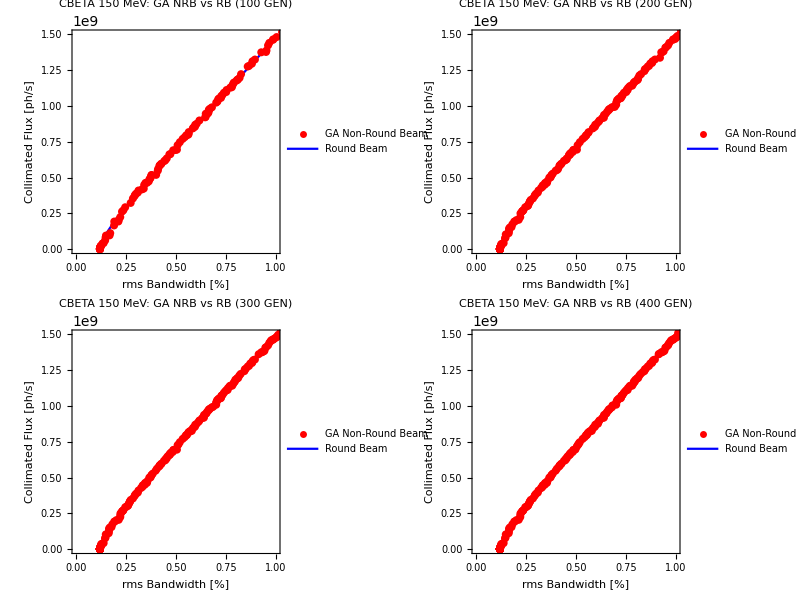

```mathematica
Grid[{{CBETAcompFBW100G,CBETAcompFBW200G},{CBETAcompFBW300G,CBETAcompFBW400G}}]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/Plots/32 Individuals/"];
```

```mathematica
Export["GA_NRB_RB_FcolBW_100G_Comparison.png",CBETAcompFBW100G];
Export["GA_NRB_RB_FcolBW_200G_Comparison.png",CBETAcompFBW200G];
Export["GA_NRB_RB_FcolBW_300G_Comparison.png",CBETAcompFBW300G];
Export["GA_NRB_RB_FcolBW_400G_Comparison.png",CBETAcompFBW400G];
```

## (β^*)_x, (β^*)_y, θ_col Variable Plots (100G)

```mathematica
CBETAcompθcolβx100G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat100G⟦All,4⟧,CBETAParetoFrontdat100G⟦All,5⟧],2],Partition[Riffle[CBETARBdat⟦All,2⟧,CBETARBdat⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Pareto Front θ_colvs β_x Parameter Space",FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA Non-Round Beam (100G, 32I)","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->Full,ImageSize->Medium];
```

```mathematica
CBETAcompθcolβy100G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat100G⟦All,4⟧,CBETAParetoFrontdat100G⟦All,6⟧],2],Partition[Riffle[CBETARBdat⟦All,2⟧,CBETARBdat⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Pareto Front θ_colvs β_y Parameter Space",FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA Non-Round Beam (100G, 32I)","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->Full,ImageSize->Medium];
```

```mathematica
CBETAcompβxβy100G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat100G⟦All,5⟧,CBETAParetoFrontdat100G⟦All,6⟧],2],βxβyRB},PlotStyle->{{PointSize[0.01],Red},Black},Joined->{False,True},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Pareto Front β_x vs β_y Parameter Space",FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA Non-Round Beam (100G, 32I)","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.34,0.85}],PlotRange->Full,ImageSize->Medium];
```

## (β^*)_x, (β^*)_y, θ_col Variable Plots (200G)

```mathematica
CBETAcompθcolβx200G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat200G⟦All,4⟧,CBETAParetoFrontdat200G⟦All,5⟧],2],Partition[Riffle[CBETARBdat⟦All,2⟧,CBETARBdat⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Pareto Front θ_colvs β_x Parameter Space",FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA Non-Round Beam (200G, 32I)","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->Full,ImageSize->Medium];
```

```mathematica
CBETAcompθcolβy200G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat200G⟦All,4⟧,CBETAParetoFrontdat200G⟦All,6⟧],2],Partition[Riffle[CBETARBdat⟦All,2⟧,CBETARBdat⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Pareto Front θ_colvs β_y Parameter Space",FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA Non-Round Beam (200G, 32I)","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->Full,ImageSize->Medium];
```

```mathematica
CBETAcompβxβy200G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat200G⟦All,5⟧,CBETAParetoFrontdat200G⟦All,6⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Pareto Front β_x vs β_y Parameter Space",FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA Non-Round Beam (200G, 32I)","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.34,0.85}],PlotRange->Full,ImageSize->Medium];
```

## (β^*)_x, (β^*)_y, θ_col Variable Plots (300G)

```mathematica
CBETAcompθcolβx300G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat300G⟦All,4⟧,CBETAParetoFrontdat300G⟦All,5⟧],2],Partition[Riffle[CBETARBdat⟦All,2⟧,CBETARBdat⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Pareto Front θ_colvs β_x Parameter Space",FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA Non-Round Beam (300G, 32I)","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->Full,ImageSize->Medium];
```

```mathematica
CBETAcompθcolβy300G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat300G⟦All,4⟧,CBETAParetoFrontdat300G⟦All,6⟧],2],Partition[Riffle[CBETARBdat⟦All,2⟧,CBETARBdat⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Pareto Front θ_colvs β_y Parameter Space",FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA Non-Round Beam (300G, 32I)","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->Full,ImageSize->Medium];
```

```mathematica
CBETAcompβxβy300G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat300G⟦All,5⟧,CBETAParetoFrontdat300G⟦All,6⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Pareto Front β_x vs β_y Parameter Space",FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA Non-Round Beam (300G, 32I)","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.34,0.85}],PlotRange->Full,ImageSize->Medium];
```

## (β^*)_x, (β^*)_y, θ_col Variable Plots (400G)

```mathematica
CBETAcompθcolβx400G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat400G⟦All,4⟧,CBETAParetoFrontdat400G⟦All,5⟧],2],Partition[Riffle[CBETARBdat⟦All,2⟧,CBETARBdat⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Pareto Front θ_colvs β_x Parameter Space",FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA Non-Round Beam (400G, 32I)","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->Full,ImageSize->Medium];
```

```mathematica
CBETAcompθcolβy400G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat400G⟦All,4⟧,CBETAParetoFrontdat400G⟦All,6⟧],2],Partition[Riffle[CBETARBdat⟦All,2⟧,CBETARBdat⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Pareto Front θ_colvs β_y Parameter Space",FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA Non-Round Beam (400G, 32I)","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->Full,ImageSize->Medium];
```

```mathematica
CBETAcompβxβy400G=ListPlot[{Partition[Riffle[CBETAParetoFrontdat400G⟦All,5⟧,CBETAParetoFrontdat400G⟦All,6⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Pareto Front β_x vs β_y Parameter Space",FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA Non-Round Beam (400G, 32I)","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.34,0.85}],PlotRange->Full,ImageSize->Medium];
```

## Variable Plots

```mathematica
CBETAcompθcolβxβy100G=Grid[{{CBETAcompθcolβx100G,CBETAcompθcolβy100G,CBETAcompβxβy100G}}];
CBETAcompθcolβxβy200G=Grid[{{CBETAcompθcolβx200G,CBETAcompθcolβy200G,CBETAcompβxβy200G}}];
CBETAcompθcolβxβy300G=Grid[{{CBETAcompθcolβx300G,CBETAcompθcolβy300G,CBETAcompβxβy300G}}];
CBETAcompθcolβxβy400G=Grid[{{CBETAcompθcolβx400G,CBETAcompθcolβy400G,CBETAcompβxβy400G}}];
```

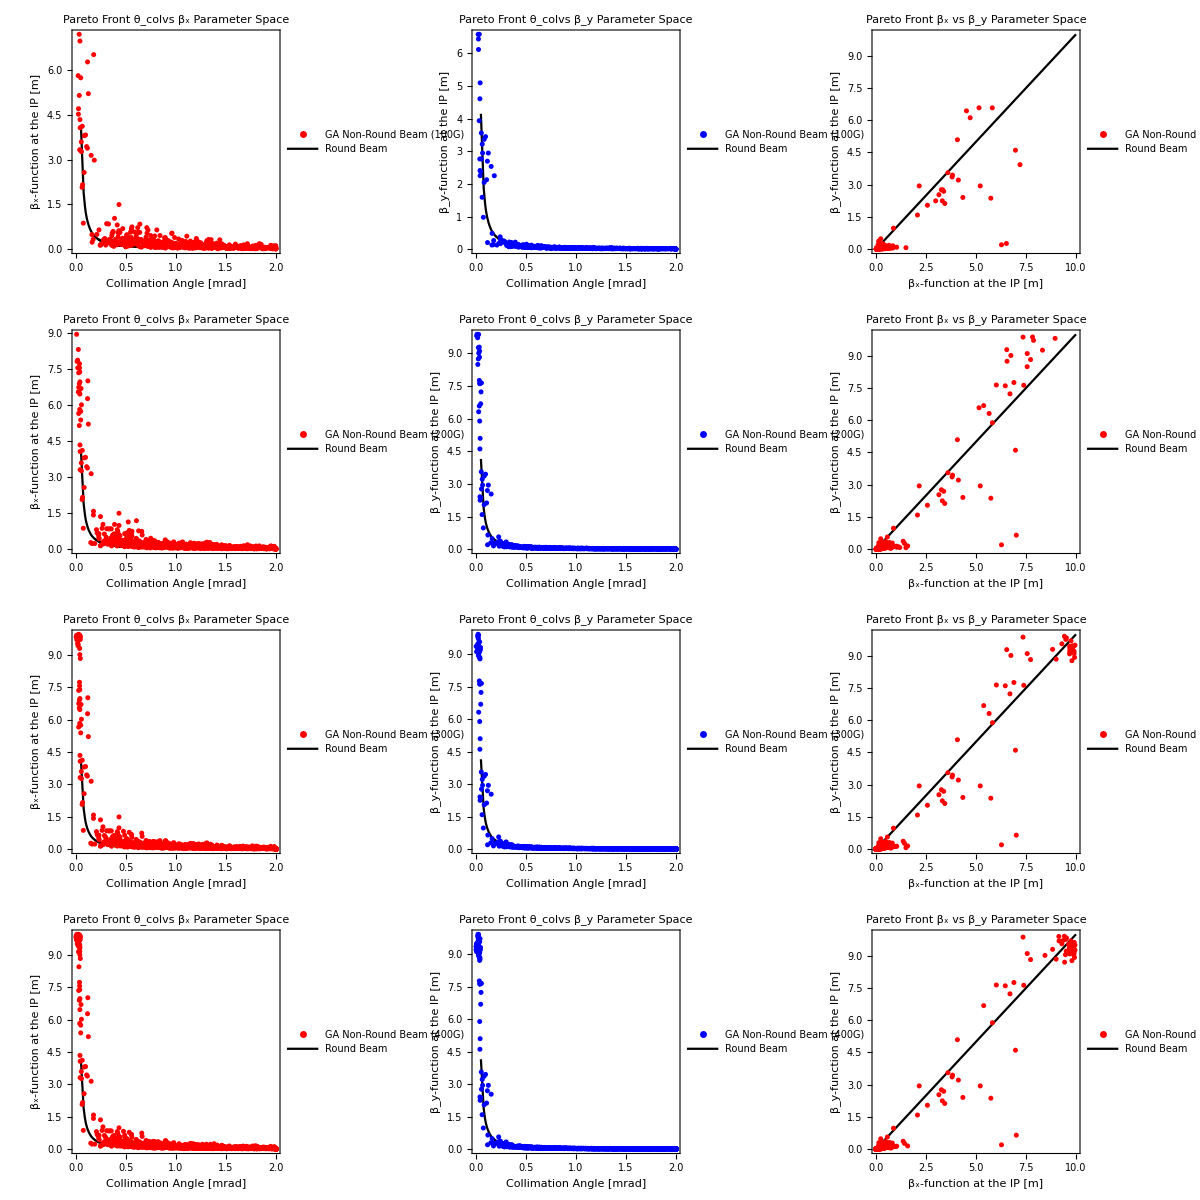

```mathematica
CBETAcompθcolβxβy=Grid[{{CBETAcompθcolβx100G,CBETAcompθcolβy100G,CBETAcompβxβy100G},{CBETAcompθcolβx200G,CBETAcompθcolβy200G,CBETAcompβxβy200G},{CBETAcompθcolβx300G,CBETAcompθcolβy300G,CBETAcompβxβy300G},{CBETAcompθcolβx400G,CBETAcompθcolβy400G,CBETAcompβxβy400G}}]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/Plots/32 Individuals/"];
```

```mathematica
Export["GA_NRB_RB_thetabetaxy_Comparison.png",CBETAcompθcolβxβy];

Export["GA_NRB_RB_thetabetaxy_100G_Comparison.png",CBETAcompθcolβxβy100G];
Export["GA_NRB_RB_thetabetaxy_200G_Comparison.png",CBETAcompθcolβxβy200G];
Export["GA_NRB_RB_thetabetaxy_300G_Comparison.png",CBETAcompθcolβxβy300G];
Export["GA_NRB_RB_thetabetaxy_400G_Comparison.png",CBETAcompθcolβxβy400G];
```

## Vary Individuals, 200 Generations

```mathematica
CBETAParetoFrontdat200G50I=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/CBETA150dat/50 Individuals/CBETA150_pareto.200","Table"];
```

```mathematica
CBETAcompFBW200G50I=ListPlot[{Partition[Riffle[CBETAParetoFrontdat200G⟦All,2⟧,-CBETAParetoFrontdat200G⟦All,3⟧],2],Partition[Riffle[CBETARBdat⟦All,1⟧,CBETARBdat⟦All,4⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Blue},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV: GA NRB vs RB (200 GEN)",PlotLegends->Placed[LineLegend[{"GA Non-Round Beam (50I)","Round Beam"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.8,0.3}],PlotRange->{{0,1},{0,1.5*10^9}},ImageSize->Large];
```

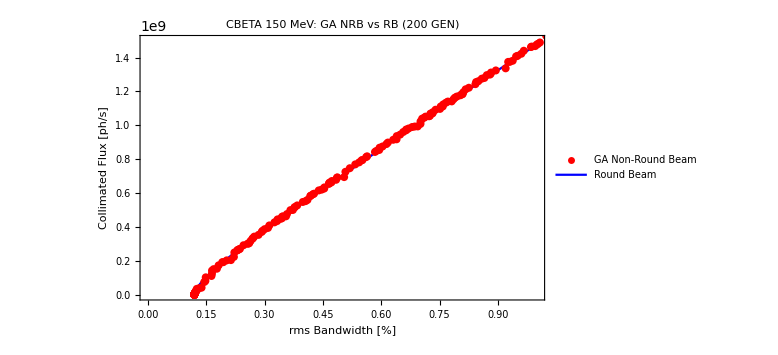
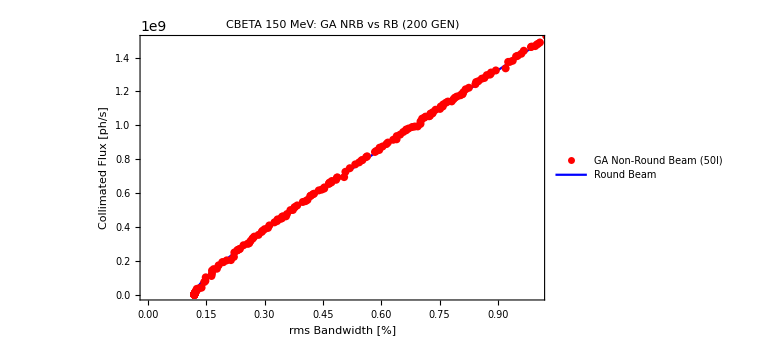
Grid[{-Graphics-,-Graphics-}]

```mathematica
Grid[{CBETAcompFBW200G,CBETAcompFBW200G50I}]
```

# DIANA Results

## Result Files

```mathematica
DIANA1072dat200G50I=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAdat/DIANA1072_pareto.200","Table"];
DIANA717dat200G50I=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAdat/DIANA717_pareto.200","Table"];
DIANA362dat200G50I=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAdat/DIANA362_pareto.200","Table"]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/DIANA"];
DIANA1072RB=<<"DIANA1072optRMS.txt";
```

## 1072 MeV Plots

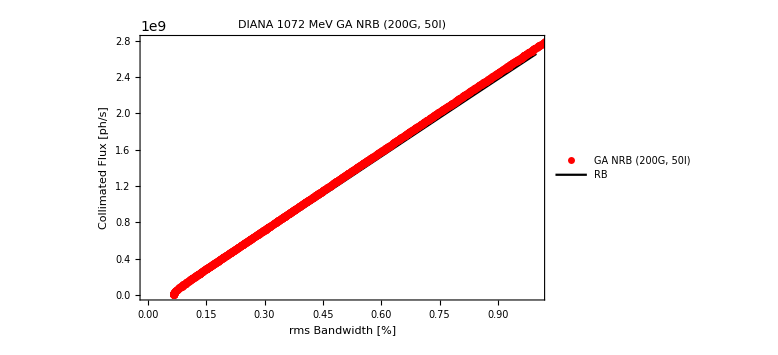

```mathematica
DIANA1072FBW200G50ILARGE=ListPlot[{Partition[Riffle[DIANA1072dat200G50I⟦All,2⟧,-DIANA1072dat200G50I⟦All,3⟧],2],Partition[Riffle[DIANA1072RB⟦All,1⟧,DIANA1072RB⟦All,4⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Joined->{False,True},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 1072 MeV GA NRB (200G, 50I)",PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.35,0.8}],PlotRange->{{0,1},{0,2.8*10^9}},ImageSize->Large]
```

```mathematica
DIANA1072FBW200G50I=ListPlot[{Partition[Riffle[DIANA1072dat200G50I⟦All,2⟧,-DIANA1072dat200G50I⟦All,3⟧],2],Partition[Riffle[DIANA1072RB⟦All,1⟧,DIANA1072RB⟦All,4⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Joined->{False,True},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 1072 MeV GA NRB (200G, 50I)",PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.35,0.8}],PlotRange->{{0,1},{0,2.8*10^9}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβx200G50I=ListPlot[{Partition[Riffle[DIANA1072dat200G50I⟦All,4⟧,DIANA1072dat200G50I⟦All,5⟧],2],Partition[Riffle[DIANA1072RB⟦All,2⟧,DIANA1072RB⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 1072 MeV PF θ_colvs β_x",FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.75,0.85}],PlotRange->{{0,0.13},{0,10}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβy200G50I=ListPlot[{Partition[Riffle[DIANA1072dat200G50I⟦All,4⟧,DIANA1072dat200G50I⟦All,6⟧],2],Partition[Riffle[DIANA1072RB⟦All,2⟧,DIANA1072RB⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 1072 PF MeV θ_colvs β_y",FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->{{0,0.13},{0,10}},ImageSize->Medium];
```

```mathematica
DIANA1072βxβy200G50I=ListPlot[{Partition[Riffle[DIANA1072dat200G50I⟦All,5⟧,DIANA1072dat200G50I⟦All,6⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.01],Green},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 1072 MeV PF β_x vs β_y",FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.34,0.85}],PlotRange->Full,ImageSize->Medium];
```

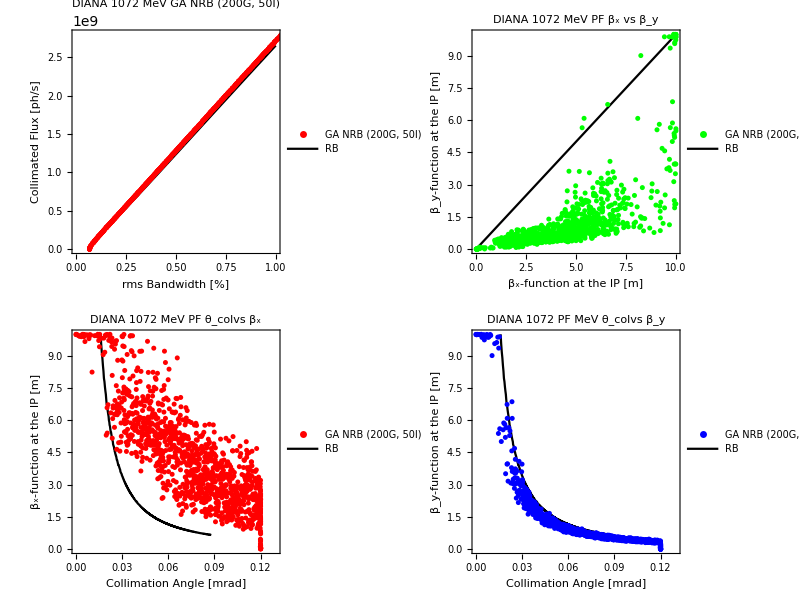

```mathematica
DIANA1072=Grid[{{DIANA1072FBW200G50I,DIANA1072βxβy200G50I},{DIANA1072θcolβx200G50I,DIANA1072θcolβy200G50I}}]
```

## 717 MeV Plots

```mathematica
DIANA717FBW200G50I=ListPlot[Partition[Riffle[DIANA717dat200G50I⟦All,2⟧,-DIANA717dat200G50I⟦All,3⟧],2],Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Blue},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 717 MeV GA NRB (200G, 50I)",PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.35,0.8}],PlotRange->{{0,1},{0,2.8*10^9}},ImageSize->Medium];
```

```mathematica
DIANA717θcolβx200G50I=ListPlot[Partition[Riffle[DIANA717dat200G50I⟦All,4⟧,DIANA717dat200G50I⟦All,5⟧],2],Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 717 MeV PF θ_colvs β_x",FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.78,0.9}],PlotRange->Full,ImageSize->Medium];
```

```mathematica
DIANA717θcolβy200G50I=ListPlot[Partition[Riffle[DIANA717dat200G50I⟦All,4⟧,DIANA717dat200G50I⟦All,6⟧],2],Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 717 PF MeV θ_colvs β_y",FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->Full,ImageSize->Medium];
```

```mathematica
DIANA717βxβy200G50I=ListPlot[{Partition[Riffle[DIANA717dat200G50I⟦All,5⟧,DIANA717dat200G50I⟦All,6⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.01],Green},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 717 MeV PF β_x vs β_y",FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.34,0.85}],PlotRange->Full,ImageSize->Medium];
```

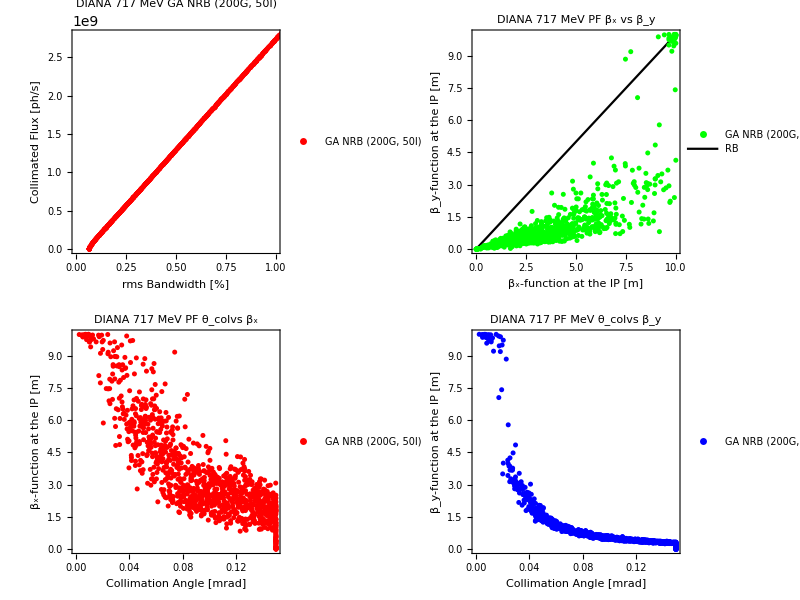

```mathematica
DIANA717=Grid[{{DIANA717FBW200G50I,DIANA717βxβy200G50I},{DIANA717θcolβx200G50I,DIANA717θcolβy200G50I}}]
```

## 362 MeV Plots

```mathematica
DIANA362FBW200G50I=ListPlot[Partition[Riffle[DIANA362dat200G50I⟦All,2⟧,-DIANA362dat200G50I⟦All,3⟧],2],Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Blue},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 362 MeV GA NRB (200G, 50I)",PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.35,0.8}],PlotRange->{{0,1},{0,2.8*10^9}},ImageSize->Medium];
```

```mathematica
DIANA362θcolβx200G50I=ListPlot[Partition[Riffle[DIANA362dat200G50I⟦All,4⟧,DIANA362dat200G50I⟦All,5⟧],2],Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 362 MeV PF θ_colvs β_x",FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.78,0.9}],PlotRange->Full,ImageSize->Medium];
```

```mathematica
DIANA362θcolβy200G50I=ListPlot[Partition[Riffle[DIANA362dat200G50I⟦All,4⟧,DIANA362dat200G50I⟦All,6⟧],2],Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 362 PF MeV θ_colvs β_y",FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->Full,ImageSize->Medium];
```

```mathematica
DIANA362βxβy200G50I=ListPlot[{Partition[Riffle[DIANA362dat200G50I⟦All,5⟧,DIANA362dat200G50I⟦All,6⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.01],Green},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 362 MeV PF β_x vs β_y",FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.34,0.85}],PlotRange->Full,ImageSize->Medium];
```

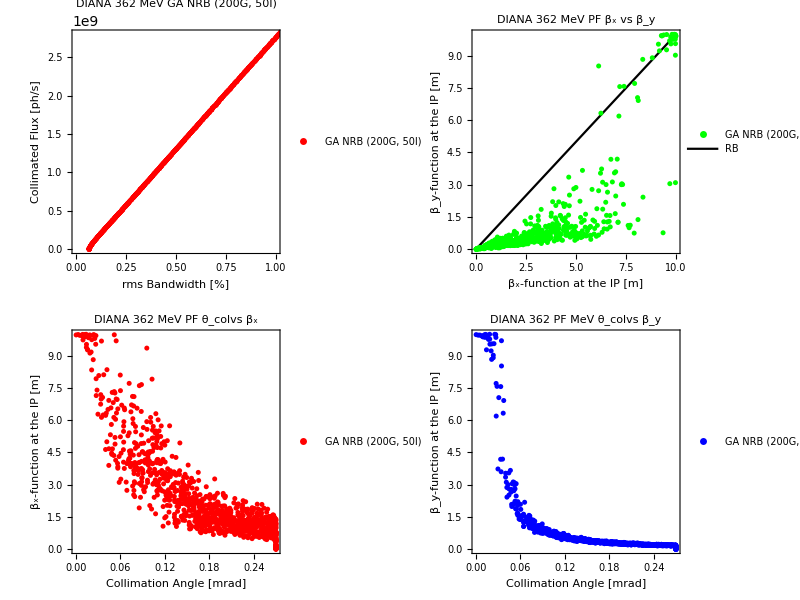

```mathematica
DIANA362=Grid[{{DIANA362FBW200G50I,DIANA362βxβy200G50I},{DIANA362θcolβx200G50I,DIANA362θcolβy200G50I}}]
```

# NEQ-SR Results

## Result Files

```mathematica
NEQSR700dat200G50I=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/NEQSRdat/NEQSR700_pareto.200","Table"];
```

```mathematica
(*SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/DIANA"];
DIANA1072RB=<<"DIANA1072optRMS.txt";*)
```

## 700 MeV Plots

```mathematica
NEQSR700FBW200G50I=ListPlot[Partition[Riffle[NEQSR700dat200G50I⟦All,2⟧,-NEQSR700dat200G50I⟦All,3⟧],2],Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Blue},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"NEQSR 700 MeV GA NRB (200G, 50I)",PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.35,0.8}],PlotRange->{{0,1},{0,2*10^9}},ImageSize->Medium];
```

```mathematica
NEQSR700θcolβx200G50I=ListPlot[Partition[Riffle[NEQSR700dat200G50I⟦All,4⟧,NEQSR700dat200G50I⟦All,5⟧],2],Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"NEQSR 700 MeV PF θ_colvs β_x",FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.78,0.9}],PlotRange->Full,ImageSize->Medium];
```

```mathematica
NEQSR700θcolβy200G50I=ListPlot[Partition[Riffle[NEQSR700dat200G50I⟦All,4⟧,NEQSR700dat200G50I⟦All,6⟧],2],Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"NEQSR 700 PF MeV θ_colvs β_y",FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->Full,ImageSize->Medium];
```

```mathematica
NEQSR700βxβy200G50I=ListPlot[{Partition[Riffle[NEQSR700dat200G50I⟦All,5⟧,NEQSR700dat200G50I⟦All,6⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.01],Green},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"NEQSR700 MeV PF β_x vs β_y",FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.34,0.85}],PlotRange->Full,ImageSize->Medium];
```

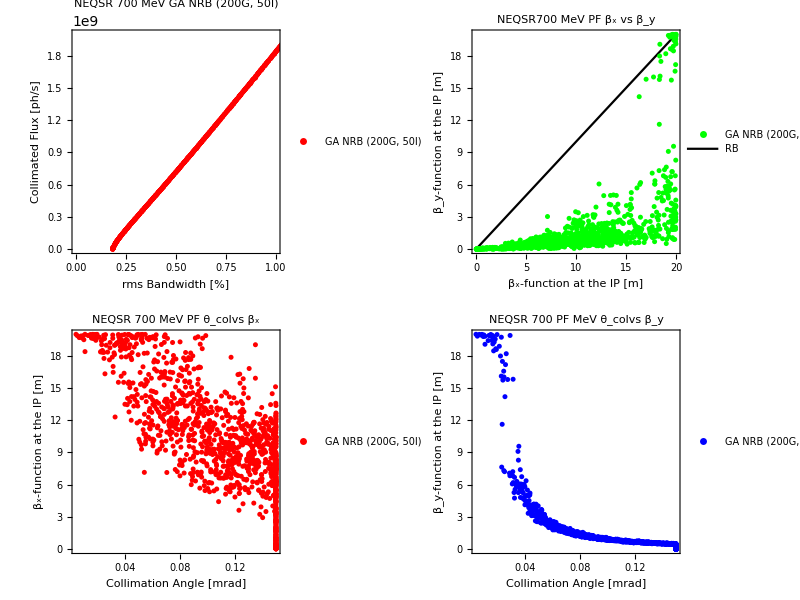

```mathematica
NEQSR700=Grid[{{NEQSR700FBW200G50I,NEQSR700βxβy200G50I},{NEQSR700θcolβx200G50I,NEQSR700θcolβy200G50I}}]
```

# Crossing Angle Investigation

## Round Beam Optimisations

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FWHM_RMS_TuningDat/DIANA/AngularCrossing"];
DIANA1072RB0=<<"DIANA1072_0_optRMS.txt";
DIANA1072RB25=<<"DIANA1072_2.5_optRMS.txt";
DIANA1072RB5=<<"DIANA1072_5_optRMS.txt";
DIANA1072RB75=<<"DIANA1072_7.5_optRMS.txt";
DIANA1072RB10=<<"DIANA1072_10_optRMS.txt";
DIANA1072RB125=<<"DIANA1072_12.5_optRMS.txt";
DIANA1072RB15=<<"DIANA1072_15_optRMS.txt";
```

```mathematica
DIANA1072FBWRB=ListPlot[{Partition[Riffle[DIANA1072RB0⟦All,1⟧,DIANA1072RB0⟦All,4⟧],2],Partition[Riffle[DIANA1072RB25⟦All,1⟧,DIANA1072RB25⟦All,4⟧],2],Partition[Riffle[DIANA1072RB5⟦All,1⟧,DIANA1072RB5⟦All,4⟧],2],Partition[Riffle[DIANA1072RB75⟦All,1⟧,DIANA1072RB75⟦All,4⟧],2],Partition[Riffle[DIANA1072RB10⟦All,1⟧,DIANA1072RB10⟦All,4⟧],2],Partition[Riffle[DIANA1072RB125⟦All,1⟧,DIANA1072RB125⟦All,4⟧],2],Partition[Riffle[DIANA1072RB15⟦All,1⟧,DIANA1072RB15⟦All,4⟧],2]},Joined->{True},PlotStyle->{Black,Red,Blue,Orange,Green,Purple,Pink},Joined->{False,True},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"F_col-BW DIANA 1072 MeV Crossing Angle RB",PlotLegends->Placed[LineLegend[{"ϕ = 0°","ϕ = 2.5°","ϕ = 5°","ϕ = 7.5°","ϕ = 10°","ϕ = 12.5°","ϕ = 15°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.15,0.7}],PlotRange->Full,ImageSize->Large];
```

```mathematica
DIANA1072βθRB=ListPlot[{Partition[Riffle[DIANA1072RB0⟦All,2⟧,DIANA1072RB0⟦All,3⟧],2],Partition[Riffle[DIANA1072RB25⟦All,2⟧,DIANA1072RB25⟦All,3⟧],2],Partition[Riffle[DIANA1072RB5⟦All,2⟧,DIANA1072RB5⟦All,3⟧],2],Partition[Riffle[DIANA1072RB75⟦All,2⟧,DIANA1072RB75⟦All,3⟧],2],Partition[Riffle[DIANA1072RB10⟦All,2⟧,DIANA1072RB10⟦All,3⟧],2],Partition[Riffle[DIANA1072RB125⟦All,2⟧,DIANA1072RB125⟦All,3⟧],2],Partition[Riffle[DIANA1072RB15⟦All,2⟧,DIANA1072RB15⟦All,3⟧],2]},Joined->{True},PlotStyle->{Black,Red,Blue,Orange,Green,Purple,Pink},Joined->{False,True},Frame->True,FrameLabel->{"Collimation Angle [mrad]","Round e^- Beam β-function [m]"},LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"β-θ_col DIANA 1072 MeV Crossing Angle RB",PlotLegends->Placed[LineLegend[{"ϕ = 0°","ϕ = 2.5°","ϕ = 5°","ϕ = 7.5°","ϕ = 10°","ϕ = 12.5°","ϕ = 15°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.85,0.7}],PlotRange->Full,ImageSize->Large];
```

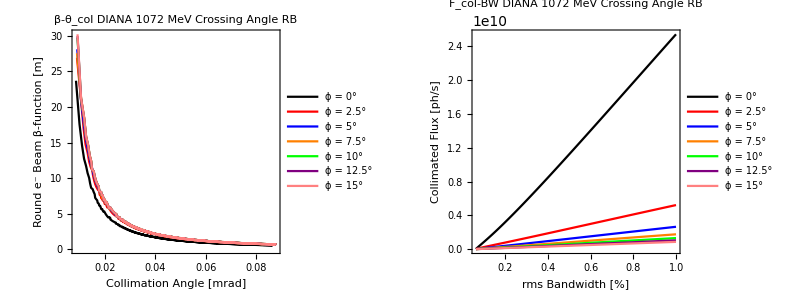

```mathematica
Grid[{{DIANA1072βθRB,DIANA1072FBWRB}}]
```

## GA NRB Optimisations (F-BW)

```mathematica
DIANA1072GA0=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAdat/CrossingAngleInvestigation/DIANA1072_0_pareto.200","Table"];
DIANA1072GA25=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAdat/CrossingAngleInvestigation/DIANA1072_2.5_pareto.200","Table"];
DIANA1072GA5=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAdat/CrossingAngleInvestigation/DIANA1072_5_pareto.200","Table"];
DIANA1072GA75=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAdat/CrossingAngleInvestigation/DIANA1072_7.5_pareto.200","Table"];
DIANA1072GA10=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAdat/CrossingAngleInvestigation/DIANA1072_10_pareto.200","Table"];
DIANA1072GA125=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAdat/CrossingAngleInvestigation/DIANA1072_12.5_pareto.200","Table"];
DIANA1072GA15=Import["C:/Users/user/Documents/Wolfram Mathematica/GA Compton Optimisations/DIANAdat/CrossingAngleInvestigation/DIANA1072_15_pareto.200","Table"];
```

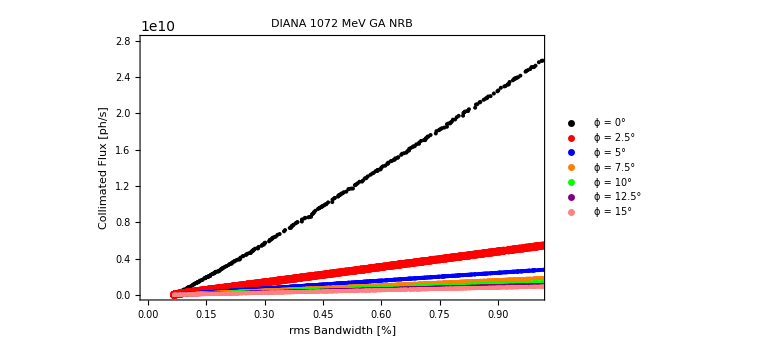

```mathematica
DIANA1072FBWGA=ListPlot[{Partition[Riffle[DIANA1072GA0⟦All,2⟧,-DIANA1072GA0⟦All,3⟧],2],Partition[Riffle[DIANA1072GA25⟦All,2⟧,-DIANA1072GA25⟦All,3⟧],2],Partition[Riffle[DIANA1072GA5⟦All,2⟧,-DIANA1072GA5⟦All,3⟧],2],Partition[Riffle[DIANA1072GA75⟦All,2⟧,-DIANA1072GA75⟦All,3⟧],2],Partition[Riffle[DIANA1072GA10⟦All,2⟧,-DIANA1072GA10⟦All,3⟧],2],Partition[Riffle[DIANA1072GA125⟦All,2⟧,-DIANA1072GA125⟦All,3⟧],2],Partition[Riffle[DIANA1072GA15⟦All,2⟧,-DIANA1072GA15⟦All,3⟧],2]},Joined->{False},PlotStyle->{{PointSize[0.005],Black},{PointSize[0.01],Red},{PointSize[0.005],Blue},{PointSize[0.005],Orange},{PointSize[0.005],Green},{PointSize[0.005],Purple},{PointSize[0.005],Pink}},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/s]"},LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 1072 MeV GA NRB ",PlotLegends->Placed[LineLegend[{"ϕ = 0°","ϕ = 2.5°","ϕ = 5°","ϕ = 7.5°","ϕ = 10°","ϕ = 12.5°","ϕ = 15°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.15,0.7}],PlotRange->{{0,1},{0,2.8*10^10}},ImageSize->Large]
```

## Comparison ϕ = 0°

```mathematica
DIANA1072FBW0=ListPlot[{Partition[Riffle[DIANA1072GA0⟦All,2⟧,-DIANA1072GA0⟦All,3⟧],2],Partition[Riffle[DIANA1072RB0⟦All,1⟧,DIANA1072RB0⟦All,4⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 0° PF ΔE_γ/E_γ vs F_col",FrameLabel->{"rms Bandwidth [%]","Collimated Flux"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{0,1},{0,2.5*10^10}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβx0=ListPlot[{Partition[Riffle[DIANA1072GA0⟦All,4⟧,DIANA1072GA0⟦All,5⟧],2],Partition[Riffle[DIANA1072RB0⟦All,2⟧,DIANA1072RB0⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 0° PF θ_colvs β_x",FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.68,0.8}],PlotRange->{{0,0.12},{0,10.5}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβy0=ListPlot[{Partition[Riffle[DIANA1072GA0⟦All,4⟧,DIANA1072GA0⟦All,6⟧],2],Partition[Riffle[DIANA1072RB0⟦All,2⟧,DIANA1072RB0⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 0° PF θ_colvs β_y",FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->{{0,0.12},{0,10.5}},ImageSize->Medium];
```

```mathematica
DIANA1072βxβy0=ListPlot[{Partition[Riffle[DIANA1072GA0⟦All,5⟧,DIANA1072GA0⟦All,6⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.01],Green},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 0° PF β_x vs β_y",FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.34,0.85}],PlotRange->{{0,10},{0,10}},ImageSize->Medium];
```

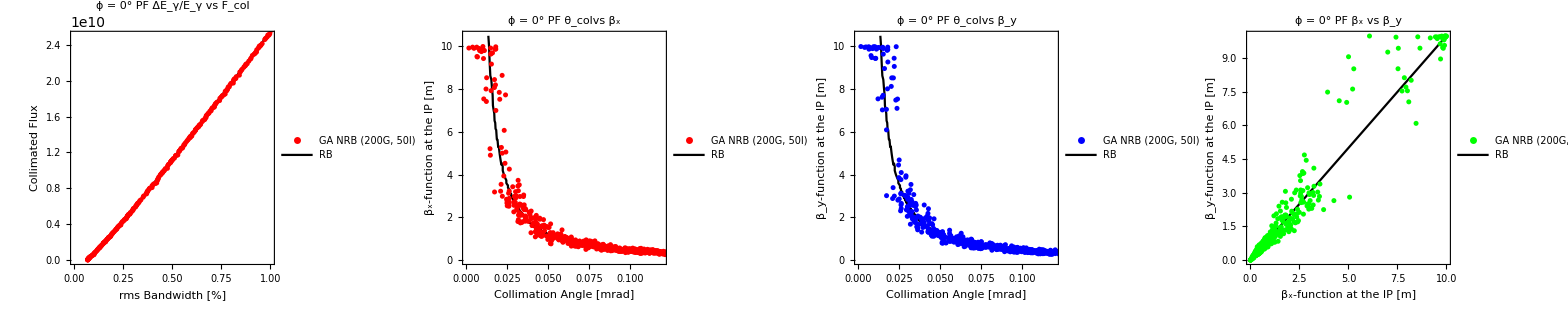

```mathematica
DIANA1072ϕ0=Grid[{{DIANA1072FBW0,DIANA1072θcolβx0,DIANA1072θcolβy0,DIANA1072βxβy0}}]
```

## Comparison ϕ = 2.5°

```mathematica
DIANA1072FBW25=ListPlot[{Partition[Riffle[DIANA1072GA25⟦All,2⟧,-DIANA1072GA25⟦All,3⟧],2],Partition[Riffle[DIANA1072RB25⟦All,1⟧,DIANA1072RB25⟦All,4⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 2.5° PF ΔE_γ/E_γ vs F_col",FrameLabel->{"rms Bandwidth [%]","Collimated Flux"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{0,1},{0,6*10^9}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβx25=ListPlot[{Partition[Riffle[DIANA1072GA25⟦All,4⟧,DIANA1072GA25⟦All,5⟧],2],Partition[Riffle[DIANA1072RB25⟦All,2⟧,DIANA1072RB25⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 2.5° PF θ_colvs β_x",FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.68,0.8}],PlotRange->{{0,0.12},{0,10.5}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβy25=ListPlot[{Partition[Riffle[DIANA1072GA25⟦All,4⟧,DIANA1072GA25⟦All,6⟧],2],Partition[Riffle[DIANA1072RB25⟦All,2⟧,DIANA1072RB25⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 2.5° PF θ_colvs β_y",FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->{{0,0.12},{0,10.5}},ImageSize->Medium];
```

```mathematica
DIANA1072βxβy25=ListPlot[{Partition[Riffle[DIANA1072GA25⟦All,5⟧,DIANA1072GA25⟦All,6⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.01],Green},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 2.5° PF β_x vs β_y",FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.34,0.85}],PlotRange->{{0,10},{0,10}},ImageSize->Medium];
```

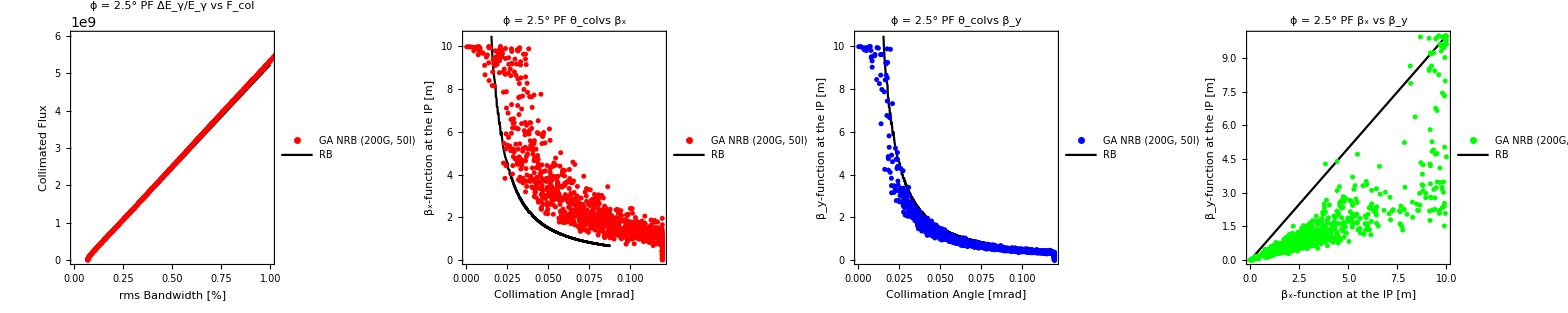

```mathematica
DIANA1072ϕ25=Grid[{{DIANA1072FBW25,DIANA1072θcolβx25,DIANA1072θcolβy25,DIANA1072βxβy25}}]
```

## Comparison ϕ = 5°

```mathematica
DIANA1072FBW5=ListPlot[{Partition[Riffle[DIANA1072GA5⟦All,2⟧,-DIANA1072GA5⟦All,3⟧],2],Partition[Riffle[DIANA1072RB5⟦All,1⟧,DIANA1072RB5⟦All,4⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 5° PF ΔE_γ/E_γ vs F_col",FrameLabel->{"rms Bandwidth [%]","Collimated Flux"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{0,1},{0,3*10^9}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβx5=ListPlot[{Partition[Riffle[DIANA1072GA5⟦All,4⟧,DIANA1072GA5⟦All,5⟧],2],Partition[Riffle[DIANA1072RB5⟦All,2⟧,DIANA1072RB5⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 5° PF θ_colvs β_x",FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.68,0.8}],PlotRange->{{0,0.12},{0,10.5}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβy5=ListPlot[{Partition[Riffle[DIANA1072GA5⟦All,4⟧,DIANA1072GA5⟦All,6⟧],2],Partition[Riffle[DIANA1072RB5⟦All,2⟧,DIANA1072RB5⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 5° PF θ_colvs β_y",FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->{{0,0.12},{0,10.5}},ImageSize->Medium];
```

```mathematica
DIANA1072βxβy5=ListPlot[{Partition[Riffle[DIANA1072GA5⟦All,5⟧,DIANA1072GA5⟦All,6⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.01],Green},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 5° PF β_x vs β_y",FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.34,0.85}],PlotRange->{{0,10},{0,10}},ImageSize->Medium];
```

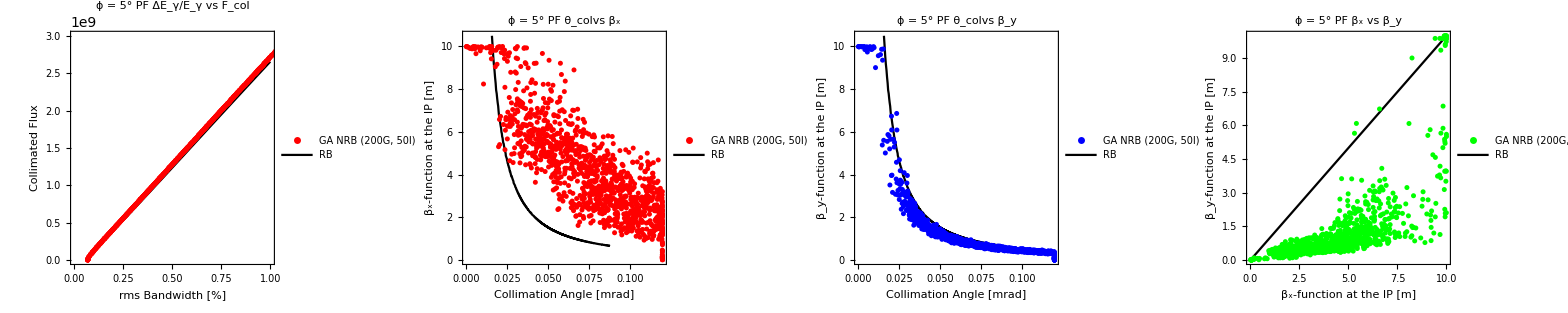

```mathematica
DIANA1072ϕ5=Grid[{{DIANA1072FBW5,DIANA1072θcolβx5,DIANA1072θcolβy5,DIANA1072βxβy5}}]
```

## Comparison ϕ = 7.5°

```mathematica
DIANA1072FBW75=ListPlot[{Partition[Riffle[DIANA1072GA75⟦All,2⟧,-DIANA1072GA75⟦All,3⟧],2],Partition[Riffle[DIANA1072RB75⟦All,1⟧,DIANA1072RB75⟦All,4⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 7.5° PF ΔE_γ/E_γ vs F_col",FrameLabel->{"rms Bandwidth [%]","Collimated Flux"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{0,1},{0,2*10^9}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβx75=ListPlot[{Partition[Riffle[DIANA1072GA75⟦All,4⟧,DIANA1072GA75⟦All,5⟧],2],Partition[Riffle[DIANA1072RB75⟦All,2⟧,DIANA1072RB75⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 7.5° PF θ_colvs β_x",FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.68,0.8}],PlotRange->{{0,0.12},{0,10.5}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβy75=ListPlot[{Partition[Riffle[DIANA1072GA75⟦All,4⟧,DIANA1072GA75⟦All,6⟧],2],Partition[Riffle[DIANA1072RB75⟦All,2⟧,DIANA1072RB75⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 7.5° PF θ_colvs β_y",FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->{{0,0.12},{0,10.5}},ImageSize->Medium];
```

```mathematica
DIANA1072βxβy75=ListPlot[{Partition[Riffle[DIANA1072GA75⟦All,5⟧,DIANA1072GA75⟦All,6⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.01],Green},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 7.5° PF β_x vs β_y",FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.34,0.85}],PlotRange->{{0,10},{0,10}},ImageSize->Medium];
```

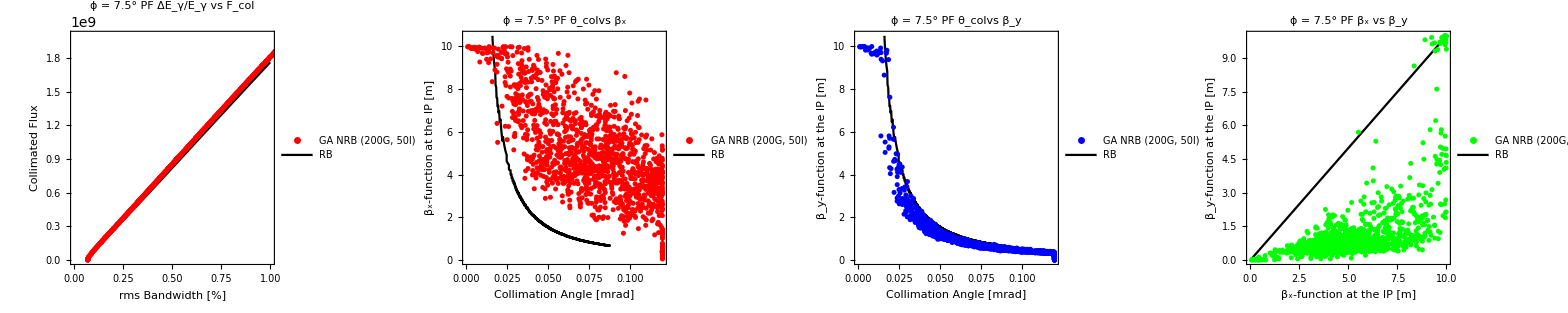

```mathematica
DIANA1072ϕ75=Grid[{{DIANA1072FBW75,DIANA1072θcolβx75,DIANA1072θcolβy75,DIANA1072βxβy75}}]
```

## Comparison ϕ = 10°

```mathematica
DIANA1072FBW10=ListPlot[{Partition[Riffle[DIANA1072GA10⟦All,2⟧,-DIANA1072GA10⟦All,3⟧],2],Partition[Riffle[DIANA1072RB10⟦All,1⟧,DIANA1072RB10⟦All,4⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 10° PF ΔE_γ/E_γ vs F_col",FrameLabel->{"rms Bandwidth [%]","Collimated Flux"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{0,1},{0,1.5*10^9}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβx10=ListPlot[{Partition[Riffle[DIANA1072GA10⟦All,4⟧,DIANA1072GA10⟦All,5⟧],2],Partition[Riffle[DIANA1072RB10⟦All,2⟧,DIANA1072RB10⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 10° PF θ_colvs β_x",FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.68,0.8}],PlotRange->{{0,0.12},{0,10.5}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβy10=ListPlot[{Partition[Riffle[DIANA1072GA10⟦All,4⟧,DIANA1072GA10⟦All,6⟧],2],Partition[Riffle[DIANA1072RB10⟦All,2⟧,DIANA1072RB10⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 10° PF θ_colvs β_y",FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->{{0,0.12},{0,10.5}},ImageSize->Medium];
```

```mathematica
DIANA1072βxβy10=ListPlot[{Partition[Riffle[DIANA1072GA10⟦All,5⟧,DIANA1072GA10⟦All,6⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.01],Green},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 10° PF β_x vs β_y",FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.34,0.85}],PlotRange->{{0,10},{0,10}},ImageSize->Medium];
```

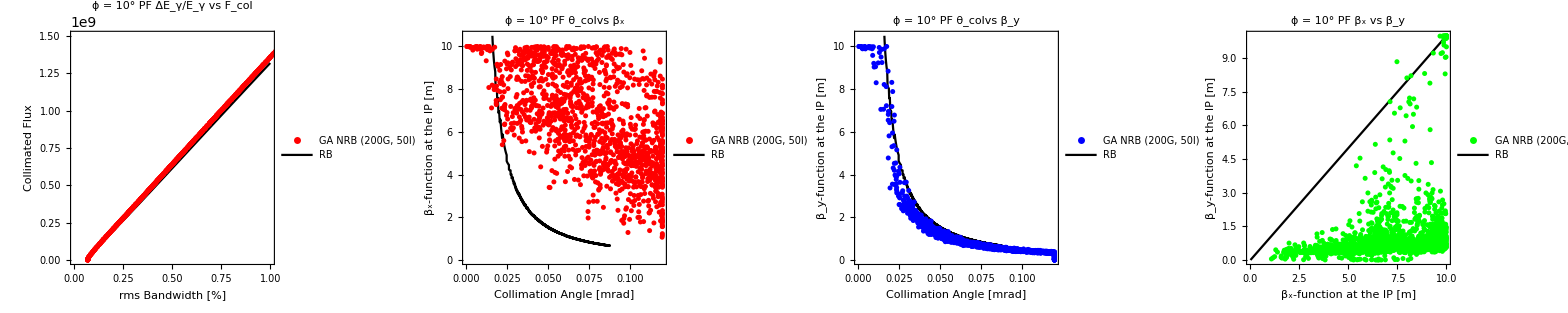

```mathematica
DIANA1072ϕ10=Grid[{{DIANA1072FBW10,DIANA1072θcolβx10,DIANA1072θcolβy10,DIANA1072βxβy10}}]
```

## Comparison ϕ = 12.5°

```mathematica
DIANA1072FBW125=ListPlot[{Partition[Riffle[DIANA1072GA125⟦All,2⟧,-DIANA1072GA125⟦All,3⟧],2],Partition[Riffle[DIANA1072RB125⟦All,1⟧,DIANA1072RB125⟦All,4⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 12.5° PF ΔE_γ/E_γ vs F_col",FrameLabel->{"rms Bandwidth [%]","Collimated Flux"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{0,1},{0,1.2*10^9}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβx125=ListPlot[{Partition[Riffle[DIANA1072GA125⟦All,4⟧,DIANA1072GA125⟦All,5⟧],2],Partition[Riffle[DIANA1072RB125⟦All,2⟧,DIANA1072RB125⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 12.5° PF θ_colvs β_x",FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.68,0.8}],PlotRange->{{0,0.12},{0,10.5}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβy125=ListPlot[{Partition[Riffle[DIANA1072GA125⟦All,4⟧,DIANA1072GA125⟦All,6⟧],2],Partition[Riffle[DIANA1072RB125⟦All,2⟧,DIANA1072RB125⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 12.5° PF θ_colvs β_y",FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->{{0,0.12},{0,10.5}},ImageSize->Medium];
```

```mathematica
DIANA1072βxβy125=ListPlot[{Partition[Riffle[DIANA1072GA125⟦All,5⟧,DIANA1072GA125⟦All,6⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.01],Green},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 12.5° PF β_x vs β_y",FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.34,0.85}],PlotRange->{{0,10},{0,10}},ImageSize->Medium];
```

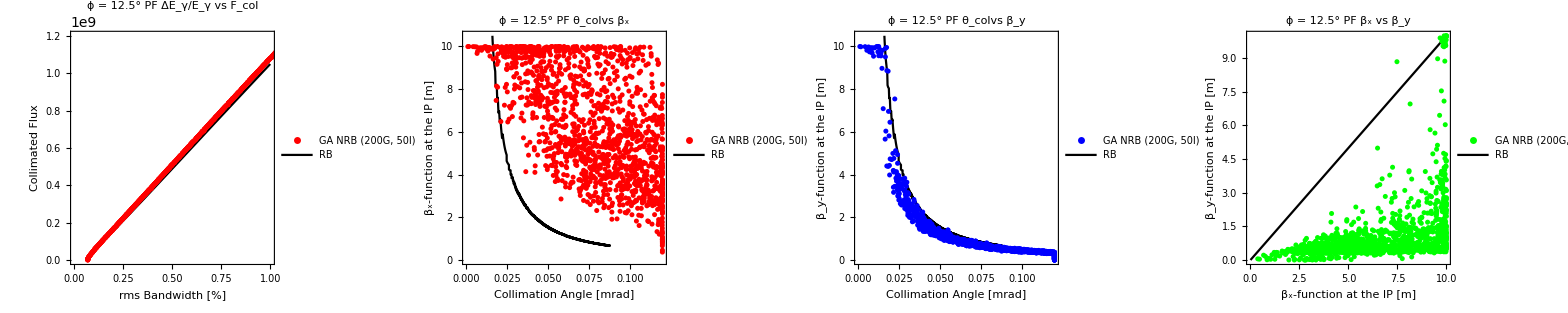

```mathematica
DIANA1072ϕ125=Grid[{{DIANA1072FBW125,DIANA1072θcolβx125,DIANA1072θcolβy125,DIANA1072βxβy125}}]
```

## Comparison ϕ = 15°

```mathematica
DIANA1072FBW15=ListPlot[{Partition[Riffle[DIANA1072GA15⟦All,2⟧,-DIANA1072GA15⟦All,3⟧],2],Partition[Riffle[DIANA1072RB15⟦All,1⟧,DIANA1072RB15⟦All,4⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 15° PF ΔE_γ/E_γ vs F_col",FrameLabel->{"rms Bandwidth [%]","Collimated Flux"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{0,1},{0,1*10^9}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβx15=ListPlot[{Partition[Riffle[DIANA1072GA15⟦All,4⟧,DIANA1072GA15⟦All,5⟧],2],Partition[Riffle[DIANA1072RB15⟦All,2⟧,DIANA1072RB15⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Red},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 15° PF θ_colvs β_x",FrameLabel->{"Collimation Angle [mrad]","β_x-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.68,0.8}],PlotRange->{{0,0.12},{0,10.5}},ImageSize->Medium];
```

```mathematica
DIANA1072θcolβy15=ListPlot[{Partition[Riffle[DIANA1072GA15⟦All,4⟧,DIANA1072GA15⟦All,6⟧],2],Partition[Riffle[DIANA1072RB15⟦All,2⟧,DIANA1072RB15⟦All,3⟧],2]},Joined->{False,True},PlotStyle->{{PointSize[0.01],Blue},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 15° PF θ_colvs β_y",FrameLabel->{"Collimation Angle [mrad]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.6,0.7}],PlotRange->{{0,0.12},{0,10.5}},ImageSize->Medium];
```

```mathematica
DIANA1072βxβy15=ListPlot[{Partition[Riffle[DIANA1072GA15⟦All,5⟧,DIANA1072GA15⟦All,6⟧],2],βxβyRB},Joined->{False,True},PlotStyle->{{PointSize[0.01],Green},Black},Frame->True,LabelStyle->{17,FontFamily->"Calibri",FontColor->Black},PlotLabel->"ϕ = 15° PF β_x vs β_y",FrameLabel->{"β_x-function at the IP [m]","β_y-function at the IP [m]"},PlotLegends->Placed[LineLegend[{"GA NRB (200G, 50I)","RB"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.34,0.85}],PlotRange->{{0,10},{0,10}},ImageSize->Medium];
```

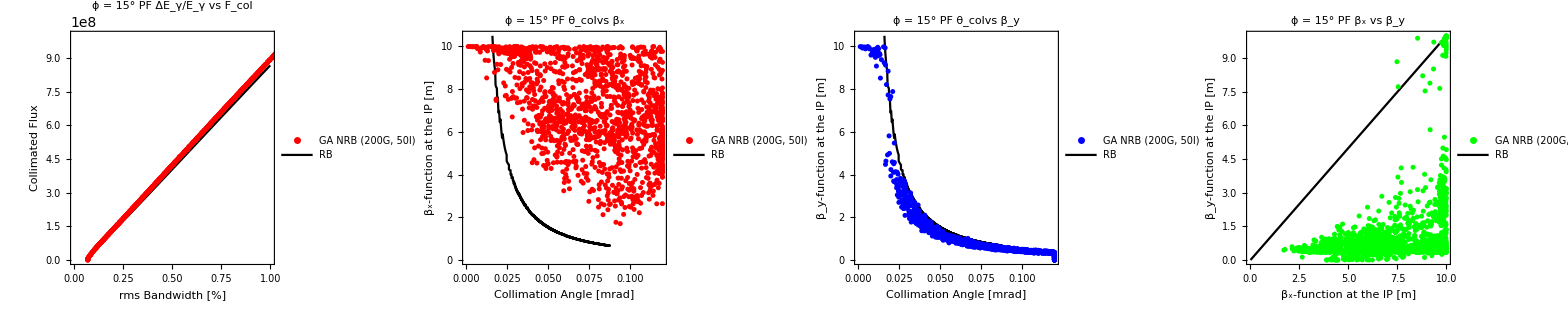

```mathematica
DIANA1072ϕ15=Grid[{{DIANA1072FBW15,DIANA1072θcolβx15,DIANA1072θcolβy15,DIANA1072βxβy15}}]
```